# 7.6

## a.

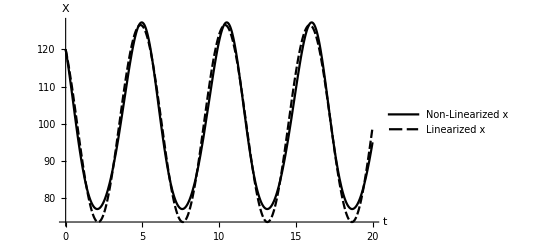
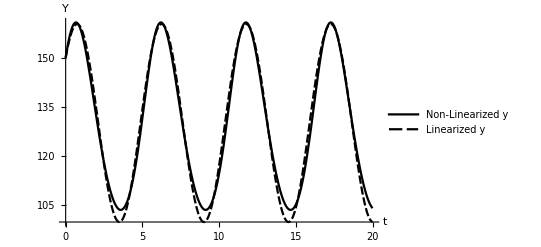
(-Graphics-
-Graphics-)

```mathematica
Module[{β1,c1,α2,c2,xi,yi,diff1,diff2,sol1,sol2},
β1=1.3;
c1=0.01;
α2=1;
c2=0.01;

diff1[xi_,yi_]=
{x'[t]==x[t](β1-c1 y[t]),x[0]==xi,
y'[t]==y[t](-α2+c2 x[t]),y[0]==yi};
sol1[xi_,yi_]:=NDSolve[diff1[xi,yi],{x,y},{t,0,20}];

diff2[xi_,yi_]=
{x'[t]==(-c1 α2)/c2(y[t]-β1/c1), x[0]==xi,
y'[t]==(c2 β1)/c1(x[t]-α2/c2),y[0]==yi};
sol2[xi_,yi_]:=DSolve[diff2[xi,yi],{x,y},t];

{{Plot[Evaluate[{x[t]/.sol1[α2/c2+20,β1/c1+20],x[t]/.sol2[α2/c2+20,β1/c1+20]}],
{t,0,20},
PlotRange->All,
PlotLegends->{"Non-Linearized x","Linearized x"},PlotTheme->"Monochrome",
AxesLabel->{"t","X"}]},
{Plot[Evaluate[{y[t]/.sol1[α2/c2+20,β1/c1+20],y[t]/.sol2[α2/c2+20,β1/c1+20]}],
{t,0,20},
PlotRange->All,
PlotLegends->{"Non-Linearized y","Linearized y"},PlotTheme->"Monochrome",
AxesLabel->{"t","Y"}]
}}//MatrixForm]
```

## b.

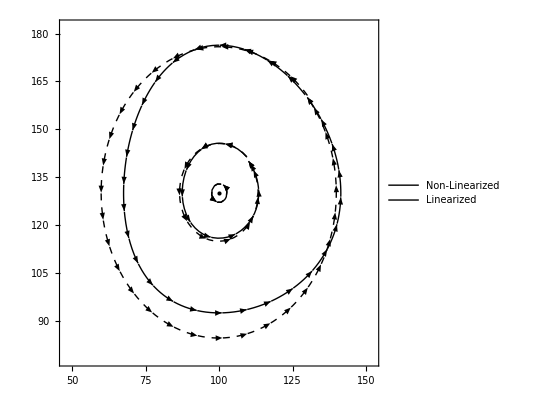
-Graphics-Phase PlaneXY

```mathematica
Module[{β1,c1,α2,c2,xi,yi,diff1,diff2,sol},
β1=1.3;
c1=0.01;
α2=1;
c2=0.01;

diff1={x(β1-c1 y),y(-α2+c2 x)};
diff2={(-c1 α2)/c2(y-β1/c1),(c2 β1)/c1(x-α2/c2)};

Labeled[Show[StreamPlot[{diff1,diff2},{x,α2/c2-50,α2/c2+50},{y,β1/c1-50,β1/c1+50},
StreamPoints->{{α2/c2+2,β1/c1+2},{α2/c2+10,β1/c1+10},{α2/c2+30,β1/c1+30}},
PlotLegends->{"Non-Linearized", "Linearized"},
StreamStyle->{Constant,Dashed},PlotTheme->"Monochrome"],
Graphics[{PointSize[Large],Point[{α2/c2,β1/c1}]}]],{"Phase Plane","X","Y"},{Top,Bottom,Left}]]
```